```mathematica
Clear["Global`*"];
```

```mathematica
λ = 1.55;
k0 = (2 Pi)/λ;
l=0;
rCore = 8.2/2;
rCladding = 125./2;
nCladding = 1.444;
dn = 0.36/100×nCladding;
nCore = nCladding+dn;
```

```mathematica
Step[x_] := UnitStep[x];
n[r_] := (Step[r] - Step[r-rCore])×nCore+(Step[r-rCore] - Step[r-rCladding])×nCladding;
Plot[n[r], {r,0,rCladding}, Exclusions->None];
```

```mathematica
u[r_,nEff_] := r k0 Sqrt[nCore^2-nEff^2];
w[r_,nEff_] := r k0 Sqrt[nEff^2-nCladding^2];
```

```mathematica
m[nEff_]:={{+BesselJ[l,u[rCore,nEff]],-BesselK[l, w[rCore,nEff]]},
{+u[rCore,nEff]D[BesselJ[l,q],{q,1}]/.{q->u[rCore,nEff]},-w[rCore,nEff] D[BesselK[l,q],{q,1}]/.{q->w[rCore,nEff]}}};
m[nEff]//MatrixForm;
```

```mathematica
nEffSolution = nEff/.FindRoot[Det[m[nEff]]==0, {nEff,nCladding+0.5×(nCore-nCladding), nCladding, nCore}]
(nEff/.FindRoot[Det[m[nEff]]==0, {nEff,nCladding+0.1×(nCore-nCladding), nCladding, nCore}])== (nEff/.FindRoot[Det[m[nEff]]==0, {nEff,nCladding+0.9×(nCore-nCladding), nCladding, nCore}]) (* проверка одномодовости *)
Det[m[nEffSolution]];
```

1.44623

True

```mathematica
C1 = 1;
C2 = C1 BesselJ[l,u[rCore, nEffSolution]]/BesselK[l, w[rCore, nEffSolution]];
```

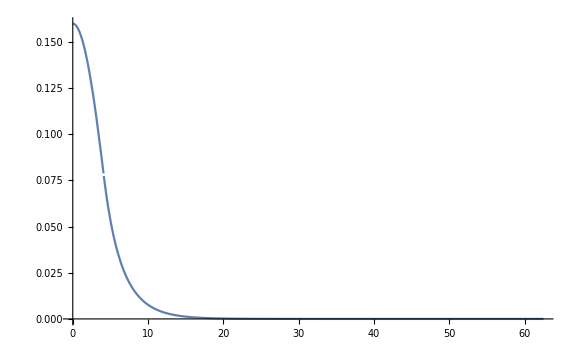

```mathematica
R[r_] := Piecewise[{
{C1 BesselJ[l,u[r, nEffSolution]], r < rCore},
{C2 BesselK[l,w[r, nEffSolution]], r ≥ rCore}}
];
RNorm[r_] := R[r]/Sqrt[NIntegrate[2 Pi rr (Abs[R[rr]])^2,{rr,0,rCladding}]];
Plot[Abs[RNorm[r]], {r,0,rCladding}, PlotRange->All, ImageSize->Large]
```

```mathematica
NIntegrate[2 Pi r Abs[RNorm[r]]^2, {r,0,rCladding}]==1;
```

длина волны отсечки с помощью проги (появляется второе решение nEff) =

```mathematica
gaussian[y0_,A_,μ_, σ_, x_] := y0 + A/(σ Sqrt[Pi/2])*Exp[-2(x-μ)^2/(σ^2)];
```

```mathematica
RNormSymmetric[r_] := RNorm[Abs[r]];
RNormSymmetricList = Parallelize[Table[{r,RNormSymmetric[r]},{r,-rCladding, rCladding,0.1}]];
```

```mathematica
nlm = NonlinearModelFit[RNormSymmetricList,gaussian[y0,A,μ,σ,r],
{{y0,Mean[Take[RNormSymmetricList[[All,2]], -50]]},
{A,RNormSymmetricList[[Ordering[RNormSymmetricList[[All, 2]],-1], 2]][[1]]},
{μ,RNormSymmetricList[[Ordering[RNormSymmetricList[[All, 2]],-1], 1]][[1]]},
{σ,10}},
r];
parametersTable = nlm["ParameterTable"]
percentageErrors = Table[
{parametersTable[[1,1,i,1]], 100*parametersTable[[1,1,i,3]]/parametersTable[[1,1,i,2]]}
,{i, 2,5,1}
]
```

| Estimate | Standard Error | t-Statistic | P-Value
y0 | 0.000488279 | 0.0000451772 | 10.8081 | 4.33129×10^-26
A | 1.40261 | 0.00217824 | 643.916 | 1.59866318989×10^-1575
μ | 5.43864×10^-17 | 0.00578284 | 9.40479×10^-15 | 1
σ | 6.98957 | 0.0118972 | 587.496 | 5.03043184145×10^-1526

{{y0,9.25232},{A,0.1553},{μ,1.06329×10^16},{σ,0.170214}}

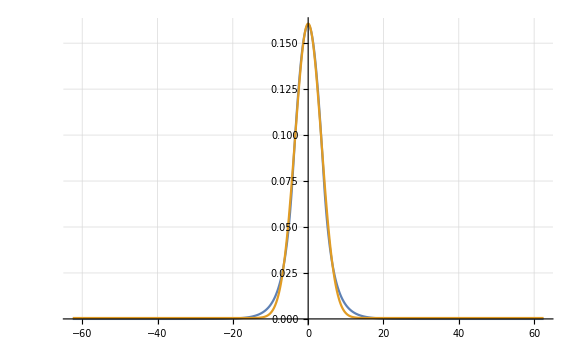

```mathematica
Plot[
{Abs[RNormSymmetric[r]],gaussian[parametersTable[[1,1,2,2]],parametersTable[[1,1,3,2]],parametersTable[[1,1,4,2]],parametersTable[[1,1,5,2]],r]}, {r,-rCladding,rCladding}, 
PlotRange-> Full,GridLines->Automatic,ClippingStyle-> Automatic, ImageSize->Large, MaxRecursion->10, PlotPoints->100, Exclusions->None]
```